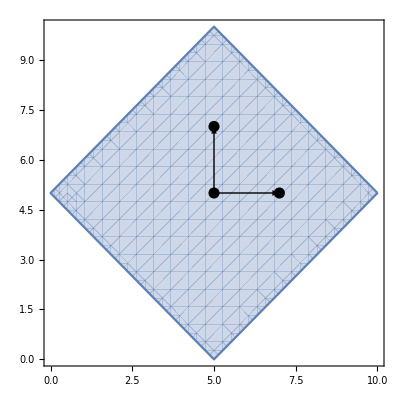

F:\Univ\_PhD\TA\MATH0462\Syllabus\5_polyhedron_2d.png

```mathematica
(* 4.1. *)
p4a=RegionPlot[x+y≥5&&x-y≤5&&-x+y≤5&&x+y≤15,{x,0,10},{y,0,10},
Epilog->{
PointSize[.02],Point[{{5,5},{7,5},{5,7}}],
Thick,Arrow[{{5,5},{7,5}}],Arrow[{{5,5},{5,7}}]
}]
Export[NotebookDirectory[]<>"5_polyhedron_2d.png",p4a]
```

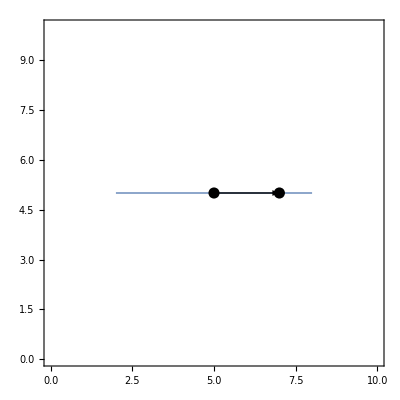

F:\Univ\_PhD\TA\MATH0462\Syllabus\5_polyhedron_1d.png

```mathematica
p4b=RegionPlot[x+y==5,{x,0,10},{y,0,10},
Epilog->{
Thick,
ColorData[97,1],
Line[{{2,5},{8,5}}],
Black,
PointSize[.02],Point[{{5,5},{7,5}}],
Arrow[{{5,5},{7,5}}]
}]
Export[NotebookDirectory[]<>"5_polyhedron_1d.png",p4b]
```